```mathematica
(*
This file calculates the numerical results in one-round-trip write algorithms W1R2 and W2R2, as shown in Section 3.2 and 3.4 in the appendix. 
*)

(*--- Section 3.2 Quantification of Visible Writes in One-Round-Trip Write ---*)

(*--- Probability of N^i(t)=k ---*)
nt[λ_,t_,k_]:=(λ*t)^(k)*E^(-λ*t)/(k!)

(*--- Probability of V^i(t,k)=1 ---*)
pv[λ_,t_,k_,n_,i_]:=Sum[nt[λ,t,j],{j,0,k}]^i*Sum[nt[λ,t,j],{j,0,k-1}]^(n-1-i)

(*--- Fig.8. The probabilities of "visible" writes from writers with different identifiers(λ=10 s^-1,t=100ms). ---*)
ListLinePlot[{Callout[Table[pv[10,0.1,1,n,0],{n,2,20 ,1}],"The writer with minimum id",Above],Callout[Table[pv[10,0.1,1,n,n-1],{n,2,20,1}],"The writer with maximum id", Right]},AxesLabel->{"Writer number","Probability"},PlotRange->{0,1},Filling->{1->{2}},Ticks->{{5,10,15,20},{0.2,0.4,0.6,0.8,1.0}}]
```

-Graphics-

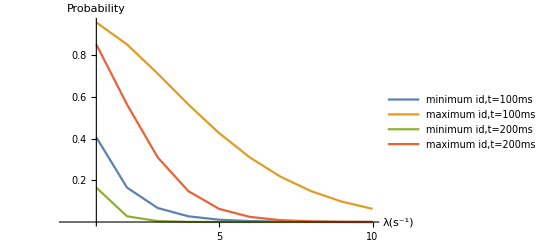

```mathematica
(*--- Fig.9. The probabilities of "visible" writes from the writer with the minimum
identifier by varying λ (Subscript[n, w]=10). ---*)
ListLinePlot[{Table[pv[λ,0.1,1,10,0],{λ,1,10}],Table[pv[λ,0.1,1,10,9],{λ,1,10}],Table[pv[λ,0.2,1,10,0],{λ,1,10}],Table[pv[λ,0.2,1,10,9],{λ,1,10}]},
PlotLegends->Placed[{"minimum id,t=100ms","maximum id,t=100ms","minimum id,t=200ms","maximum id,t=200ms"},{Right,Top}],AxesLabel->{"λ(s^-1)","Probability"},AxesOrigin->{1,0},Ticks->{{5,10,15,20},{0.2,0.4,0.6,0.8,1.0}}]
```

```mathematica
(*--- TABLE 3
Numerical results on the probabilities of "invisible" writes in one-round-write algorithms without extra information in acknowledgement(λ=10 s^-1,t=100ms). ---*)
Table[1-pv[10,0.1,1,n,i],{n,2,10},{i,0,n-1}]
```

{{0.632121,0.264241},{0.864665,0.729329,0.458659},{0.950213,0.900426,0.800852,0.601703},{0.981684,0.963369,0.926737,0.853475,0.70695},{0.993262,0.986524,0.973048,0.946096,0.892193,0.784386},{0.997521,0.995042,0.990085,0.98017,0.96034,0.92068,0.84136},{0.999088,0.998176,0.996352,0.992705,0.98541,0.97082,0.94164,0.883279},{0.999665,0.999329,0.998658,0.997316,0.994633,0.989265,0.97853,0.957061,0.914122},{0.999877,0.999753,0.999506,0.999013,0.998025,0.996051,0.992102,0.984204,0.968407,0.936814}}

```mathematica
(*--- Section 3.4 Improvement of One-Round-Trip Write Algorithms ---*)

(*--- Probability of U^i(t)=1 ---*)
pu[λ_,t_,n_,i_]:=Sum[nt[λ,t,j],{j,0,2}]^i*Sum[nt[λ,t,j],{j,0,1}]^(n-1-i)


Table[1-pu[10,0.1,n,i],{n,2,10},{i,0,n-1}]
```

```mathematica
(*--- Fig.10. The probabilities of "visible" writes from writers with different identifiers using the improved update acknowledgement (λ=10 s^-1,t=100ms). ---*)
ListLinePlot[{Callout[Table[pu[10,0.1,n,0],{n,2,50 }],"The writer with minimum id",Above],Callout[Table[pu[10,0.1,n,n-1],{n,2,50 }],"The writer with maximum id", Right]},Filling->{1->{2}},AxesLabel->{"Writer number","Probability"},Ticks->{{10,20,30,40,50},{0.2,0.4,0.6,0.8,1.0}}]
```

-Graphics-

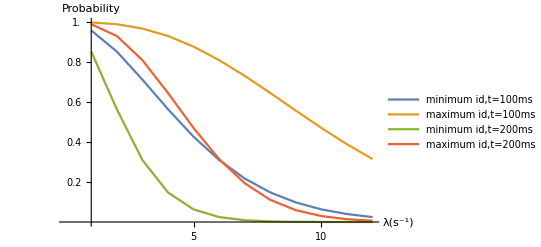

```mathematica
(*--- Fig.11. The probabilities of "visible" writes from the writer with maximum
/minimum identifier by varying λ using the improved update acknowledgement(Subscript[n, w]=10). ---*)
ListLinePlot[{Table[pu[λ,0.1,10,0],{λ,1,12}],Table[pu[λ,0.1,10,9],{λ,1,12}],Table[pu[λ,0.2,10,0],{λ,1,12}],Table[pu[λ,0.2,10,9],{λ,1,12}]},
PlotLegends->Placed[{"minimum id,t=100ms","maximum id,t=100ms","minimum id,t=200ms","maximum id,t=200ms"},{Right,Top}],AxesLabel->{"λ(s^-1)","Probability"},AxesOrigin->{1,0},Ticks->{{5,10,15,20},{0.2,0.4,0.6,0.8,1.0}}]
```

```mathematica
(*--- TABLE 3
Numerical results on the probabilities(lower bound) of "invisible" writes in one-round-write algorithms if sequence number is included in acknowledgement(λ=10 s^-1,t=100ms). ---*)
Table[1-pu[10,0.1,n,i],{n,2,10},{i,0,n-1}]
```

{{0.264241,0.0803014},{0.458659,0.323324,0.154154},{0.601703,0.502129,0.377662,0.222077},{0.70695,0.633687,0.542109,0.427636,0.284545},{0.784386,0.730482,0.663103,0.578878,0.473598,0.341997},{0.84136,0.8017,0.752125,0.690156,0.612695,0.515869,0.394836},{0.883279,0.854099,0.817624,0.77203,0.715037,0.643796,0.554745,0.443431},{0.914122,0.892652,0.865815,0.832269,0.790336,0.73792,0.6724,0.5905,0.488125},{0.936814,0.921018,0.901272,0.87659,0.845738,0.807172,0.758965,0.698707,0.623383,0.529229}}